```mathematica
Clear["Global`*"]
```

```mathematica
maxIterations = 500;
```

```mathematica
cobweb[map_,x0In_, xRange_]:=Module[{diagonal, curve, line, line2,web={}, x0, x1},

diagonal =  Graphics[
{Gray,Line[{{xRange[[1]],xRange[[1]]}, {xRange[[2]],xRange[[2]]}}]}
];

curve = Plot[map[x],{x,xRange[[1]], xRange[[2]]},Frame->True, Axes -> False, AspectRatio-> 1, PlotRange->xRange];

x0 = x0In;
For[i=0,i<maxIterations,i++,
x1 = map[x0];
line = Graphics[
{Red,Line[{{x0,x0},{x0,x1}}]}
];
line2 = Graphics[
{Red,Line[{{x0,x1}, {x1,x1}}]}
];
x0 = x1;
AppendTo[web,line];
AppendTo[web,line2];
];

Show[curve,web,diagonal]
]
```

```mathematica
gaussMap[x_]:= Exp[-4.9 x^2] + -.58

r = 3.4;
logisticMap[x_]:= r x (1 - x)
```

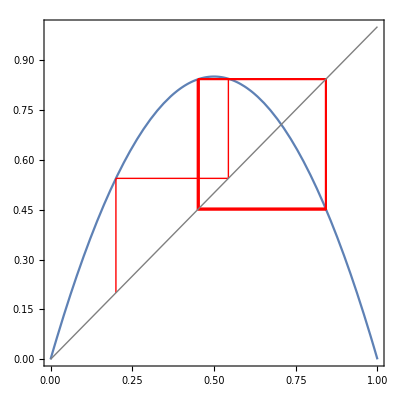

```mathematica
cobweb[logisticMap,.2, {0, 1}]
```

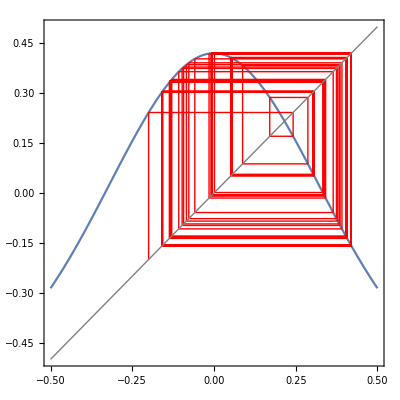

```mathematica
cobweb[gaussMap, -.2, {-.5, .5}]
```